```mathematica
(* Define default values for parameteres here *)
δ10 = -0.5;
δ20 = 0.5;
Ω=0.0;
α=1;
ϕc=-π/2;
ω21= 1;
θ=0;
η=1;
ϕp=0;
tmin=0;
tmax=6;
step=0.001;
```

```mathematica
G[x_]:=Return[-α Exp[I π/4]/Sqrt[4π(x)^3]];
eqs={
H1[s](1+I δ10+G[s])==Ω Exp[I ϕc]H2[s-I ω21]-H2[s]*G[s]*η+Sin[θ]Exp[I ϕp],
H2[s](1+I δ20+G[s])==-Ω Exp[-I ϕc]H1[s+I ω21]-H1[s]*G[s]*η+Cos[θ]
};
vars={H1[s],H2[s]};
sol=NSolve[eqs,vars];

data=Table[Flatten@{s,Abs[H1[s]/.sol]^2,Abs[H2[s]/.sol]^2},{s,tmin,tmax,step}];
(*leqs=Simplify[LaplaceTransform[eqs,t,s]];*)
```

ListPlot::lpn: {{{167.572+2.00857×10^-15 ⅈ,161.089+2.80105×10^-15 ⅈ},{2.50719-50.7775 ⅈ,-2.56197-53.8559 ⅈ},{1.29839-24.0185 ⅈ,-1.35317-28.2982 ⅈ},«45»,{-0.0266124-1.04473 ⅈ,-0.0281645-1.13468 ⅈ},{-0.026595-1.02338 ⅈ,-0.0281819-1.11152 ⅈ},«5951»}} is not a list of numbers or pairs of numbers.

ListPlot[{{167.572+2.00857×10^-15 ⅈ,161.089+2.80105×10^-15 ⅈ},{2.50719-50.7775 ⅈ,-2.56197-53.8559 ⅈ},{1.29839-24.0185 ⅈ,-1.35317-28.2982 ⅈ},5996,{1.29839+24.0185 ⅈ,-1.35317+28.2982 ⅈ},{2.50719+50.7775 ⅈ,-2.56197+53.8559 ⅈ}}]
 |  |  |  |

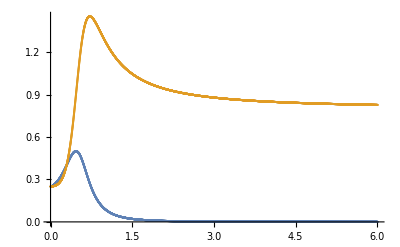

```mathematica
data2=Table[{data[[i,1]],data[[i,2]]},{i,1,Length[data]}];
data3=Table[{data[[i,1]],data[[i,3]]},{i,1,Length[data]}];
dd=Fourier[data2];
ListPlot[dd]
ListPlot[{data2,data3}]
```

```mathematica
data
```

{{0.,0.981748 Abs[(-0.159577+0.478731 ⅈ)+(19+1) 1-(0.239365+0.0797885 ⅈ) H2[0.-1. ⅈ]]^2,0.981748 Abs[(0.478731-0.159577 ⅈ)-(0.0797885+0.239365 ⅈ) H1[0.+1. ⅈ]+(0.0797885+0.239365 ⅈ) H2[0.-1. ⅈ]]^2},5999,{6.,0.000967013 Abs[1]^2,0.000967013 Abs[(19+1)+1+1]^2}}
 |  |  |  |

```mathematica
(* Numerical Solution of the problem and density matrix evaluation part *)
(*Export["data.txt",data,"TSV"];*)

For[i=1,i≤Length[data],i++,
ρv11=data[[i,2]]*Conjugate[data[[i,2]]];
ρv12=data[[i,2]]*Conjugate[data[[i,3]]];
ρv21=data[[i,3]]*Conjugate[data[[i,2]]];
ρv22=data[[i,3]]*Conjugate[data[[i,3]]];
ρv33=1-ρv11-ρv22;
ttv[i]=data[[i,1]];
ρ[i]={ttv[i],{{ρv11,ρv12,0},{ρv21,ρv22,0},{0,0,ρv33}}};
];
ρ11=Table[ρ[i][[2,1,1]],{i,1,Length[data]}];
ρ12=Table[ρ[i][[2,1,2]],{i,1,Length[data]}];
ρ21=Table[ρ[i][[2,2,1]],{i,1,Length[data]}];
ρ22=Table[ρ[i][[2,2,2]],{i,1,Length[data]}];
ρ33=Table[ρ[i][[2,3,3]],{i,1,Length[data]}];
tt=Table[ttv[i],{i,1,Length[data]}];
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h1'[0.]==(0.+0.5 ⅈ) h1[0.]-Integrate[Times[«6»],{«3»}],h2'[0.]==(0.-0.5 ⅈ) h2[0.]-Integrate[Times[«6»],{«3»}],h2[0]==1,h1[0]==0},{h1,h2},{0.,0,6},StartingStepSize→0.001,Method→{FixedStep,Method→ExplicitEuler}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h1'[0.]==(0.+0.5 ⅈ) h1[0.]-Integrate[Times[«6»],{«3»}],h2'[0.]==(0.-0.5 ⅈ) h2[0.]-Integrate[Times[«6»],{«3»}],h2[0]==1,h1[0]==0},{h1,h2},{0.,0,6},StartingStepSize→0.001,Method→{FixedStep,Method→ExplicitEuler}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{h1'[0.001]==0.+(0.+0.5 ⅈ) h1[0.001],h2'[0.001]==0.-(0.+0.5 ⅈ) h2[0.001],h2[0]==1,h1[0]==0},{h1,h2},{0.001,0,6},StartingStepSize→0.001,Method→{FixedStep,Method→ExplicitEuler}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

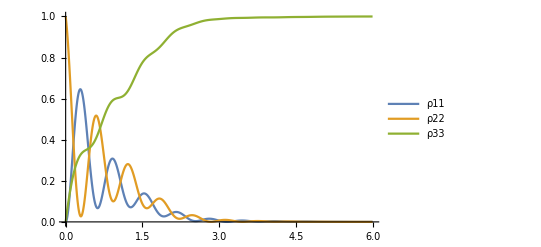

```mathematica
ListLinePlot[{Transpose@{tt,Re[ρ11]},Transpose@{tt,Re[ρ22]},Transpose@{tt,Re[ρ33]}},PlotRange->All,PlotLegends->{"ρ11","ρ22","ρ33"}]
```

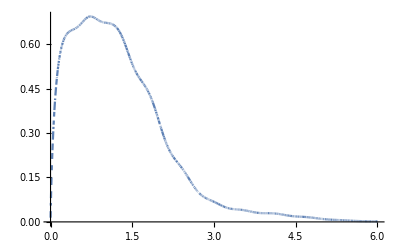

```mathematica
entropy=Array[0,0];
eigval=Array[0,0];
eigvec=Array[0,0];
For[i=1,i≤Length[data],i++,
tmp=ρ[i][[2]];
AppendTo[eigval,Eigenvalues[tmp]];
AppendTo[eigvec,Eigenvectors[tmp]];
AppendTo[entropy,-N[Total[Eigenvalues[tmp]*Log[Eigenvalues[tmp]]]]];
];
ListLinePlot[Transpose@{tt,entropy},PlotRange->All]
```

```mathematica
N[Tr[ρ]]
```

Tr[ρ]

```mathematica
DownValues[ρ]
```

{HoldPattern[ρ[1]]:>{0.,{{0.+0. ⅈ,0.+0. ⅈ,0},{0.+0. ⅈ,1.+0. ⅈ,0},{0,0,0.+0. ⅈ}}},5999,HoldPattern[ρ[6001]]:>{6.,{{0.000154489+0. ⅈ,0.0000303564+6.96523×10^-6 ⅈ,0},{0.0000303564-6.96523×10^-6 ⅈ,6.27892×10^-6+0. ⅈ,0},{0,0,0.999839+0. ⅈ}}}}
 |  |  |  |

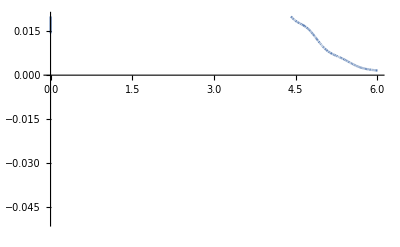

```mathematica
ListLinePlot[Transpose@{tt,entropy},PlotRange->{All,{-0.05,0.02}}]
```

```mathematica
eigval[[1]]
eigvec[[1]]
```

{1.,0.,0.}

{{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
fisher  thetaP va phi
```

fisher phi thetaP va